# Midterm 3

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 5

Two Martians are having a water balloon launching contest. They are standing on a position that has a colatitude of 120 degrees (meaning a polar angle of 120 degrees from the geographic north pole). A small target has been placed 2 km directly west of where they are standing. The first Martian, who has taken Physics 121 but not Physics 321, decides to launch the balloon due west with a 45 degree angle above the horizontal and an initial launch speed of 86.267 m/s. The second Martian, who has taken Physics 321, smiles to herself, already knowing that she will win the competition because her less-experienced friend does not know about the Coriolis force. The goal of this problem is to determine how far away the water balloon lands from the target. The figures below illustrate the situation.
-Graphics-



-Graphics-


-Graphics-

Important information:
Let z be up, x be due east, and y be due north (this is the convention used in the textbook and lecture when deriving the equations for projectile motion).
The acceleration due to gravity near the surface of Mars is 3.721 m/s^2 (you may assume this includes any minor modifications due to the centrifugal force).
The atmosphere on Mars is very thin, so you may neglect any drag forces.
Mars takes 24.6598 hours to complete one rotation about its axis.

m = 0.5 kg is the mass of the water balloon.
theta = 120 degrees is the angle from the geographic north pole.
Omega is the angular speed of Mars (you must calculate this).

```mathematica
Quit[]
Clear["'*"]
```

## Part A: Qualitative Analysis (5 points)

Will the landing point of the water balloon be south of the target or north of the target?
South of the target

Will the landing point of the water balloon be east of the target or west of the target?
East of the target

## Part B: Set up the equations and initial conditions (7 points)

Various values are given to you below, but you must calculate the value for Omega based on information given in the problem. (1 point)

```mathematica
m=0.5;
g=3.721;
theta=120*Pi/180; (* colatitude *)
alpha=45*Pi/180; (* launch angle *)
v0=86.267; (* launch speed *)
Omega= (2*Pi)/(24.6598*60*60)(* angular speed of Mars *)
```

0.0000707763

Now write down the equations of motion appropriate for this situation, taking into account the rotation of Mars. (3 points)

```mathematica
Xeq=m*x''[t]==(2*m*Omega*(y'[t]*Cos[theta]-z'[t]*Sin[theta]))
Yeq=m*y''[t]==(-2*m*Omega*x'[t]*Cos[theta])
Zeq=m*z''[t]==-g*m+2*m*Omega*x'[t]*Sin[theta]
```

0.5 x''[t]==0.0000707763 (-1/2 y'[t]-1/2 √3 z'[t])

0.5 y''[t]==0.0000353881 x'[t]

0.5 z''[t]==-1.8605+0.0000612941 x'[t]

And now provide the initial conditions. (3 points)

```mathematica
x0=0;
xdot0=-v0*Cos[alpha];
y0=0;
ydot0=0;
z0=0;
zdot0=v0*Sin[alpha];
```

## Part C: Solve for the trajectory and interpret it (8 points)

Solve the equations. (2 points)

```mathematica
sol=NDSolve[{Xeq,Yeq,Zeq,x[0]==x0,y[0]==y0,z[0]==z0,x'[0]==xdot0,y'[0]==ydot0,z'[0]==zdot0},{x,y,z},{t,0,40}];
```

Determine how far it misses in the x direction. (2 points)

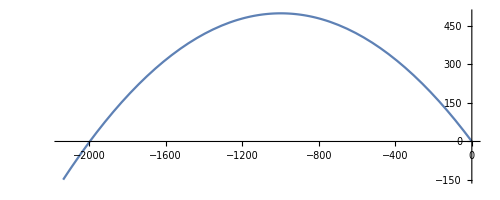

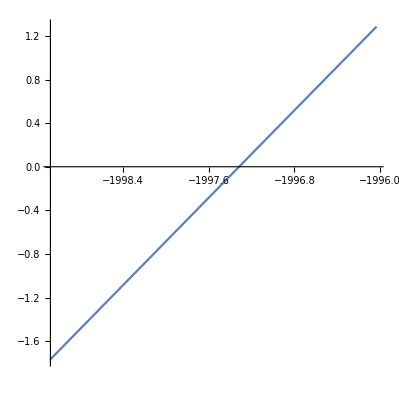

```mathematica
ParametricPlot[{x[t],z[t]}/.sol,{t,0,35}]

(* Now zoom in as appropriate to find your answer to the nearest 0.1 meters *)
ParametricPlot[{x[t],z[t]}/.sol,{t,32.7,32.75}]
```

Answer to the nearest 0.1 m: Δx = landing value - target value = landing value - (- 2000 m) = -1997.3-(-2000) = 2.7 meters

Determine how far it misses in the y direction. (2 points)

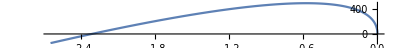

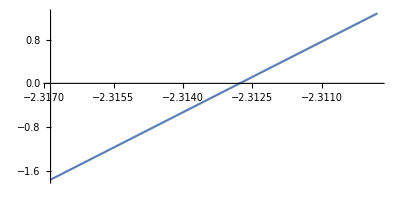

```mathematica
ParametricPlot[{y[t],z[t]}/.sol,{t,0,35},AspectRatio->0.1]
(* Now zoom in as appropriate to find your answer to the nearest 0.1 meters *)
ParametricPlot[{y[t],z[t]}/.sol,{t,32.7,32.75},AspectRatio->0.5]
```

Answer to the nearest 0.1 m: Δy = landing value - target value = landing value - 0 = -2.3128 - 0 = -2.3128 meters

In terms of the cardinal directions (north, south, east, west), describe where the landing point of the water balloon is relative to the target. (2 points) 
(Type your answer here.) The balloon’s landing point shifted 2.7 meters in the eastward direction and to the south by 2.3128 meters compared to its inertial frame landing point.

## Additional work for any of the written problems (label each one clearly)

```mathematica
Quit[]
```

```mathematica
(*Problem 3*)
Jxy=((M*4)/(3*L^2))*Integrate[Integrate[x*y,{y,-x,(1/2)*x}],{x,0,L}];
Jxx=((M*4)/(3*L^2))*Integrate[Integrate[x*x,{y,-x,(1/2)*x}],{x,0,L}];
Jyy=((M*4)/(3*L^2))*Integrate[Integrate[y*y,{y,-x,(1/2)*x}],{x,0,L}];
Jzz=0;
Jxz=0;
Jyz=0;
mu = (L^2*M)/8;
I1={{mu,mu,0},{mu,4*mu,0},{0,0,5*mu}};
Eigensystem[{{mu,mu,0},{mu,4*mu,0},{0,0,5*mu}}]
wvec=w*{1/Sqrt[2],-1/Sqrt[2],0};
Simplify[1-(1/2)*(5-Sqrt[13])]
Simplify[(w/2)*(1/Sqrt[2])*((3*L^2*M*w)/(8*Sqrt[2]))]
```

-(L^2 M)/8

(L^2 M)/2

(L^2 M)/8

{{(5 L^2 M)/8,1/16 (5+√13) L^2 M,1/16 (5-√13) L^2 M},{{0,0,1},{1/2 (-3+√13),1,0},{1/2 (-3-√13),1,0}}}

1/2 (-3+√13)

3/32 L^2 M w^2

```mathematica
(*problem 4*)
M = {{m,0,0},{0,m,0},{0,0,m}};
K = {{2*k,-k,0},{-k,2*k,-k},{0,-k,2*k}};
{{2*k-w^2*m,-k,0},{-k,2*k-w^2*m,-k},{0,-k,2*k-w^2*m}}//MatrixForm
det=Det[{{2*k-w^2*m,-k,0},{-k,2*k-w^2*m,-k},{0,-k,2*k-w^2*m}}];
Solve[det==0,w]
Eigensystem[Inverse[M].K]
```

(2 k-m w^2 | -k | 0
-k | 2 k-m w^2 | -k
0 | -k | 2 k-m w^2)

{{w→-√((2 k)/m-(√2 k)/m)},{w→√((2 k)/m-(√2 k)/m)},{w→-√((2 k)/m+(√2 k)/m)},{w→√((2 k)/m+(√2 k)/m)},{w→-(√2 √k)/(√m)},{w→(√2 √k)/(√m)}}

{{((2+√2) k)/m,(2 k)/m,((2-√2) k)/m},{{1,-√2,1},{-1,0,1},{1,√2,1}}}